```mathematica
Clear[t, m,n,o,p]
f[a_, b_, c_, d_, e_, x_]=e+d x+c x^2+b x^3+a x^4
df[a_, b_, c_, d_, e_, x_] = D[f[a, b, c, d, e, x], {x, 1}]
ddf[a_, b_, c_, d_, e_, x_] =D[f[a, b, c, d, e, x], {x, 2}]
energyAtAPoint[a_, b_, c_, d_, e_, x_]=(ddf[a, b, c, d, e, x])^2
energy[a_,b_,c_, d_, e_, t_] = Integrate[energyAtAPoint[a, b, c, d, e, x], {x, 0, t}]
constraints={
f[a, b, c, d, e, 0]==m,
df[a, b, c, d, e, 0]==n,
f[a, b, c, d, e, t]==o,
df[a, b, c, d, e, t]==p
};

Print["constraintsSolutions:"]
constraintsSolutions = Solve[constraints, {b, c, d, e}]
Print["Constraints with solutions:"]
constraintsSimplified = constraints /.constraintsSolutions[[1]]
energyWithSolutions[a_, t_] = Evaluate[energy[a, b, c, d, e, t] /.constraintsSolutions[[1]]]
Print["Energy function:"]
energySimplified[a_, t_] = Simplify[energyWithSolutions[a, t]]
Print["solution: (a, b, c, d, e)"]

(*without loss of generality: t is always 1*)

amin = ArgMin[{energySimplified[a, 1]}, a]
bmin = First[Evaluate[b /. constraintsSolutions /. {t->1,a->amin}] ] 
cmin =  First[Evaluate[c /. constraintsSolutions /. {t->1,a->amin, b->bmin} ]  ]
dmin =  First[Evaluate[d /. constraintsSolutions /. {t->1,a->amin, b->bmin, c->cmin} ]  ]
emin =  First[Evaluate[e /. constraintsSolutions /. {t->1,a->amin, b->bmin, c->cmin, d->dmin} ] ] 
Print["Check:"]
Simplify[constraints /. {t->1,a->amin, b->bmin, c->cmin, d->dmin, e->emin}] 
Print["Target function:"]
f [amin, bmin, cmin, dmin, emin, x]
```

e+d x+c x^2+b x^3+a x^4

d+2 c x+3 b x^2+4 a x^3

2 c+6 b x+12 a x^2

(2 c+6 b x+12 a x^2)^2

4 c^2 t+12 b c t^2+12 b^2 t^3+16 a c t^3+36 a b t^4+(144 a^2 t^5)/5

constraintsSolutions:

{{b→-(-2 m+2 o-n t-p t+2 a t^4)/t^3,c→-(3 m-3 o+2 n t+p t-a t^4)/t^2,d→n,e→m}}

Constraints with solutions:

{True,True,True,n+4 a t^3-(2 (3 m-3 o+2 n t+p t-a t^4))/t-(3 (-2 m+2 o-n t-p t+2 a t^4))/t==p}

(144 a^2 t^5)/5-16 a t (3 m-3 o+2 n t+p t-a t^4)+(4 (3 m-3 o+2 n t+p t-a t^4)^2)/t^3-36 a t (-2 m+2 o-n t-p t+2 a t^4)+(12 (3 m-3 o+2 n t+p t-a t^4) (-2 m+2 o-n t-p t+2 a t^4))/t^3+(12 (-2 m+2 o-n t-p t+2 a t^4)^2)/t^3

Energy function:

(4 (15 m^2+15 o^2-15 o (n+p) t+15 m (-2 o+(n+p) t)+t^2 (5 n^2+5 n p+5 p^2+a^2 t^6)))/(5 t^3)

solution: (a, b, c, d, e)

0

2 m+n-2 o+p

-3 m-2 n+3 o-p

n

m

Check:

{True,True,True,True}

Target function:

m+n x+(-3 m-2 n+3 o-p) x^2+(2 m+n-2 o+p) x^3

```mathematica
bestWay =Evaluate[ArgMin[{energySimplified[a, 5],constraintsSimplified},{a}]]
```

{0}

```mathematica
ArgMin[{Function[{a',5'},energy[a,b,c,d,e,5]/.constraintsSolutions⟦1⟧],{True,True,m+n t+a t^4+t^3 (-2 a t-(-2 m+2 o-n t-p t)/t^3)+t^2 (a t^2-(3 m-3 o+2 n t+p t)/t^2)==o,n+4 a t^3+3 t^2 (-2 a t-(-2 m+2 o-n t-p t)/t^3)+2 t (a t^2-(3 m-3 o+2 n t+p t)/t^2)==p}},{a}]
```

ArgMin[{Function[{a',5'},energy[a,b,c,d,e,5]/.constraintsSolutions⟦1⟧],{True,True,a t^4+t^3 (-20/t^3-2 a t)+t^2 (30/t^2+a t^2)==10,4 a t^3+3 t^2 (-20/t^3-2 a t)+2 t (30/t^2+a t^2)==0}},{a}]

```mathematica
Quit[]
```

{-1.4-0.5 x+8.5 x^2-5.3 x^3}

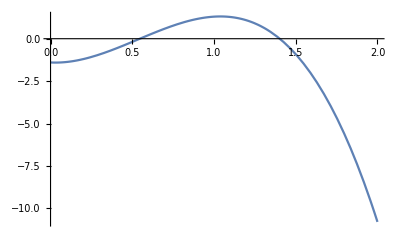

```mathematica
clear[m,n,o,p]
m:=-1.4
n:=-0.5
o:=1.3
p:=0.6
targetF[x_] = f[amin, bmin, cmin, dmin, emin, x]
Plot[targetF[x],{x,0,2}]
```